# Mathematica Quickstart Guide

## Notebooks and cells

### Videos

Please make sure you do the entire notebook below. If you like video instruction, feel free to also watch any of the videos found at 
http://www.wolfram.com/broadcast/screencasts/handsonstart/ 

“Notebooks” overlaps with the information provided in this section, “Notebooks and cells”. Some of the other videos overlap significantly with information provided below or in other assigned notebooks.

### Interacting with Mathematica through the notebook interface

Mathematica is split into two parts: the front-end and the kernel.  You interact with Mathematica through the front end with a document called a notebook.   A notebook consists of a series of cells. Textual cells contain static text, whether it be a document title, section title, or the text you are reading right now. This is the word processor part. You can use it for creating documents like this one, but you can also use it just for documenting your calculations or keeping notes to yourself as you do exploratory data analysis. Input cells contain stuff that you want to send to the Mathematica kernel, which does the computations. Once the contents of an input cell is sent to the kernel (i.e. evaluated), the output of the computation (if any) is displayed in an output cell. For example, here is an input cell and the corresponding output cell.

```mathematica
(x+2)(x+1)
```

(1+x) (2+x)

First, notice that the input and output cells are identified by cell labels at the left. Second, notice that the kernel didn’t have much to say about this input, besides that it prefers to have the terms of polynomials ordered from lowest degree to highest. That’s because there isn’t any obviously better or simpler form for this expression than the form we provided it in. We can specifically ask Mathematica to expand this out using the built-in function Expand:

```mathematica
Expand[(x+2)(x+1)]
```

2+3 x+x^2

##### Practice: Creating and evaluating cells

Now you try it. Create a new cell directly below this one, either by using the down arrow key to move below the current cell or by clicking the mouse between this cell and the next. In your new cell, type the function Factor followed by matching open and close square brackets, then between the square brackets type the result of the Expand above, 2+3 x+x^2. Since you are typing in an input cell (the default) your typing should come out in Courier font, like the input cells shown above. To send it to the Mathematica kernel for evaluation, make sure your cursor is somewhere in the cell you want to evaluate, hold down the shift key, and press return. You should instantly get (1+x)(2+x), i.e., a factored form of 2+3 x+x^2 in an output cell. Below that, make a new cell by using the down arrow and convert it to a text cell by the menu sequence Format -> Style -> Text. (A faster way to do this is to hold down the Alt or Command key and press 7). Now when you type, you should get a sans serif font like the one this text is in. Please enter a comment on how the result from Factor compares to the input we originally gave to Expand.

```mathematica
Factor[2 + 3x + x^2]
```

(1+x) (2+x)

Hello America, and welcome to my first Mathematica comment section! How exciting. The result from factor is the factored version of the result from expand.

##### Practice: Creating, using, and saving a new notebook

Whenever you start something new, you’ll want to create a new notebook. You can do that when you first open Mathematica from the top left of the welcome screen, or if you’re in the middle of a session, by the menu sequence File -> New -> Notebook. Create a new notebook, then do the following

Go to the Palettes menu and select “Writing Assistant”. This palette serves more-or-less as a word processing menu that allows you to do the usual things, like choosing font sizes and colors, paragraph style, etc. One of the main differences with an ordinary word processor is that the document is organized in cells so there are ways to change cell properties, such as the background shading, as well as cell styles, which are collections of properties. Another difference is that formatting of mathematical expressions is very convenient via the “Typesetting” section of the palette.

In your new notebook, use the Format -> Style to apply the Title style to the first cell and type into it to give your notebook a title, such as “Michael’s First Mathematica Notebook”.

In your new notebook, create a new cell and compute the factorial of 101 by evaluating the expression 101!. Then do the same for 100!. Now divide the first result by the second. You can reference the previous results using the labels, such Out[1] or Out[2].

Use the menu sequence File -> Save and save your notebook as a file called FirstNotebook-Name where “Name” is your name. Now double-clicking on this file should open it up in Mathematica.

### How to think about Notebooks

Most people think about programming in terms of writing code in one file, then either compiling the file into something you can run from a command line or loading it into an interactive interpreter, where you can call each of the individual functions you’ve defined and see the result. One of the possible uses of a Mathematica notebook is as an interpreter for Mathematica expressions. To stick most closely to the normal model, you would write your code in a separate file, which typically has the extension “.m” and is referred to in Mathematica documentation as a either a script file or a package file (the difference is not important for now). Recently, they have rebranded the Mathematica programming language as the Wolfram Language so you may see that terminology, too. You can edit the file using a text editor such as Emacs or Vi, or you can use Wolfram Workbench, an IDE (Integrated Development Environment) based on the open-source Eclipse. In this class, we strongly encourage development in Workbench. 

You can develop code in Workbench and use a notebook as the interpreter. If you use a new notebook cell for each interaction and save your notebook at the end, all the interactions are saved for later reference. Often most of them are not worth saving because you’re just trying to figure out how to get something to work and once it does the failed attempts are no longer useful. Thus, it is often worthwhile to reuse the same input cell, editing and reevaluting it until you get a result you want to save. The output from each evaluation of a cell will overwrite the output of the previous evaluation. It’s also worth deleting some of the less interesting cells you’ve created at the end of the session.

##### Practice: Reusing a notebook cell

The following computation creates a list, or table, of the exact values of x Log2[x] for several values of x. Place your cursor in the cell below and use shift-return to evaluate it.

```mathematica
Table[x Log2[x], {x, 1, 10}]
```

{0,2,(3 Log[3])/Log[2],8,(5 Log[5])/Log[2],(6 Log[6])/Log[2],(7 Log[7])/Log[2],24,(9 Log[9])/Log[2],(10 Log[10])/Log[2]}

```mathematica
Table[ N(xLog2[x]), {x, 1, 10}]
```

{N xLog2[1],N xLog2[2],N xLog2[3],N xLog2[4],N xLog2[5],N xLog2[6],N xLog2[7],N xLog2[8],N xLog2[9],N xLog2[10]}

```mathematica
Table[N(x Log2[x], {x, 1, 10})]
```

Syntax::sntxf: "(" cannot be followed by "xLog2[x],{x,1,10})".

```mathematica
Table[N[x Log2[x]], {x, 1, 10}]
```

{0.,2.,4.75489,8.,11.6096,15.5098,19.6515,24.,28.5293,33.2193}

By using the second argument for the Table function, {x, 1, 10}, (I am assuming) “x” was defined as numbers 1 through 10 (including both 1 and 10). These numbers were iteratively put in the original log2 function.

Suppose you wanted the numbers expressed as floating point approximations, rather than ratios of natural logarithms. To do so, you need to wrap the function N around the x Log2[x]. Edit the contents of the input cell above so that you will get floating point approximations and use shift-return to evaluate it. Note how the new output overwrites the old. Now create a new text cell between the output and this paragraph and write a comment in red (you can change the font color using the Writing Assistant palette) regarding the effect of the second argument we gave to Table, namely, {x, 1, 10}. If you’re not sure, you can either experiment or you can look up  the documentation on Table by using the menu sequence Help -> Wolfram Documentation and typing Table into the search bar. ■

To delete a cell, or change anything about its formatting, you must select the cell by selecting the innermost bracket to the right of the cell. Cells are organized into a hierarchical structure which is indicated by the bracketing at right, so if you want you can select higher level cells such as the one for an entire section or subsection of a notebook.

##### Practice: Selecting cells

```mathematica
Select this cell and then use the "Format" dropdown menu to format it as an input cell.
```

## Mathematica documentation

Your Mathematica installation comes with vast amounts of documentation. To access it, use the menu sequence Help -> Wolfram Documentation. The most important thing in the Wolfram Documentation is the search bar at the top. You can think of this as a web browser. Type in whatever it is you want to know about, look over the list of pages that comes back, and start reading the ones that look promising. You will do this many times and spend a lot of time reading the documentation. This can be a frustrating process because you will often get a lot of reference information but not the introduction to the big concepts needed to understand the system. All I can say is, “I’m sorry” and “Get used to it”. I will try to fill in the big concepts whenever I can, but you should expect to spend a fair amount of time being confused and a fair amount of time browsing from one help page to another trying to get a foothold. 

There are several categories of documentation pages, including

Tutorials. These are very useful and include some of the basic concepts you will need. I suggest reading a tutorial first whenever you can find a relevant one.  You can see an example by going to the doc center, typing or pasting tutorial/InterruptingCalculations into the search bar, and pushing return.

How Tos. You can see an example by going to the doc center, typing or pasting howto/StopAComputation into the search bar, and pushing return. Unfortunately, simply typing in “How to stop a computation” draws a blank.

Mathematica guides.

Reference material, especially on built-in Mathematica functions and symbols. The reference pages for built-in functions (e.g. Table) have a fixed structure. In the search bar at the top of the doc center or any other documentation page, search Table now -- the reference page should display right away.

In large, black type you’ll see the title of the page, which is the name of the function.

Above that, and to the right, are drop-down menus for accessing related documentation by type -- in this case, there is a menu listing several related tutorials, another one listing guides, and a “See Also” which lists related reference pages. Quite often, it will be worth your while to look at the guides and tutorials before reading reference pages, although sometimes the reference pages will give you what you want faster. You’ll have to develop your own personal documentation reading style over time.

Below the title you’ll see one or more cells with yellow backgrounds, each showing a template for how you can call the function with various argument types and a very brief description of what each one does. This is useful mainly if you already know one way to use the function and you’re looking for variants.

Below the yellow boxes is a section called Details which is closed by default. More often than not, you’ll want to leave that closed until you’ve looked at part of the next section, titled Examples.

The Examples section shows examples of what you can do with the function. In some cases you will be able to use these as templates for building your expressions. It is often useful to read through at least the subsection titled Basic Examples. I find that I am tempted to keep reading examples, but there are often a lot of them and it is not always as useful to read them all as to glance over the Details section and then look for related tutorials. However, if you know this is the function you want to use and you’re trying to do something complicated with it, reading all the examples can be helpful.

You can also look up a function’s usage directly in a notebook by typing ?FunctionName, where FunctionName is the name of the function.  For example,

```mathematica
?Table
```

Table[expr,{i_max}] generates a list of i_max copies of expr. 
Table[expr,{i,i_max}] generates a list of the values of expr when i runs from 1 to i_max. 
Table[expr,{i,i_min,i_max}] starts with i=i_min. 
Table[expr,{i,i_min,i_max,di}] uses steps di. 
Table[expr,{i,{i_1,i_2,…}}] uses the successive values i_1, i_2, ….
Table[expr,{i,i_min,i_max},{j,j_min,j_max},…] gives a nested list. The list associated with i is outermost.

Another resource for finding information on functions is with the Help->Function Navigator.  The Function Navigator lists a hierarchical view of Mathematica’s functions.
I don’t see this.

##### Practice: Reading documentation 1

Go to the reference page for Table.

In a new text cell below this one, write the names of all the tutorials that are in the list of tutorials at the top of the page. You’ll have to change the style of your cell to “text” so it doesn’t get interpreted as an input cell.

Tutorials: Repetitive Operations, Making Tables of Values, Evaluation in Iteration Functions, Vectors and Matrices, Tensors

Read the basic examples on the Table reference page. In a new input cell below this one, write an expression using Table that, when evaluated, outputs a list of the cubes of all the integers between 1 and 12, inclusive. (You can use the notation x^3 for x cubed.) In another new input cell, write an expression that uses Table to list the cubes of the numbers 0.2, 0.3, ..., 0.7.

```mathematica
Table[i^3, {i, 1, 12}]
```

{1,8,27,64,125,216,343,512,729,1000,1331,1728}

```mathematica
Table[i^3, {i, .2, .7, .1}]
```

{0.008,0.027,0.064,0.125,0.216,0.343}

### Incorporated reading

There’s no point to my trying to rewrite tutorials and documentation on all the stuff that’s already included in the Mathematica documentation. Instead, I will do some introducing, sequencing, and provision of relevant Practices and Exercises. In between these, I’ll ask you to read particular documentation pages as though they were incorporated into this document. That means as soon as you see a section titled “Incorporated reading,” you should go off and read whatever pages are referenced there, then come back and continue working with this document. Right now, please read

howto/CreateLists. You can also get an html version of this page from a web browser at http://reference.wolfram.com/mathematica/howto/CreateLists.html. This site, which contains all the documentation with the obvious mapping to the URL, might occasionally be useful if you don’t have Mathematica open or can’t open it for some reason.

##### Practice: Making lists and vectors

From now on, do all assignments that are in Mathematica notebooks by creating new cells immediately below the assignment, unless it is specified that they should be done in a new notebook. Save your modified copy of the notebook containing the assignments by appending a dash followed by your name to the end of the original filename, before the “.nb” suffix. By affixing your name, you affirm that you typed any modifications to the original file yourself. Copying modified assignment files or portions thereof, or distributing them to others, or placing them in a location where others can easily grab them, is considered cheating. You can get help and advice, but you must do all the typing yourself.

Make the same two lists of cubes you did with Table, but now do it  with Range. As demonstrated in the “howto” for creating lists, use Range to create a list of numbers and then apply the cubing operation to the entire list.

Create a “matrix” (i.e. list of lists) with 7 rows and 3 columns containing random integers between 17 and 23. First display it as a list of lists, and then in matrix form.

```mathematica
List[17,23]
```

{17,23}

```mathematica
List[RandomInteger[17, 23]]
```

{{15,10,6,3,10,6,9,4,5,6,9,3,2,9,6,2,11,0,17,15,8,3,5}}

```mathematica
List[RandomInteger[Range[17, 23], 21]]
```

RandomInteger::parb: {17,18,19,20,21,22,23} should have between 0 and 2 parameters.

{RandomInteger[{17,18,19,20,21,22,23},21]}

```mathematica
m = RandomInteger[Range[17,23], {7, 3}]
```

RandomInteger::parb: {17,18,19,20,21,22,23} should have between 0 and 2 parameters.

RandomInteger[{17,18,19,20,21,22,23},{7,3}]

```mathematica
m = RandomInteger[{17, 23}, {7, 3}]
```

{{22,22,22},{22,20,18},{20,23,19},{19,20,22},{23,18,20},{22,17,20},{21,17,19}}

```mathematica
MatrixForm[m]
```

(22 | 22 | 22
22 | 20 | 18
20 | 23 | 19
19 | 20 | 22
23 | 18 | 20
22 | 17 | 20
21 | 17 | 19)

### Evaluate all input cells

From now on, wherever you see an input cell that does not have a corresponding output cell in a notebook I have distributed, you should evaluate it and look at the output. Make sure you understand why that input gave that output. If you forget to evaluate an input cell then future cells may not evaluate the way they are supposed to, so please check carefully for input cells and make sure to evaluate them.

## Programming in Mathematica

### Videos

Please make sure you do the entire notebook below. If you like video instruction, feel free to also watch the video “Basic Calculations”, which can be found at 
http://www.wolfram.com/broadcast/screencasts/handsonstart/ .

### Defining variables and functions

In order to understand variables and functions, we need to touch briefly on how the kernel works. If you are used to interpreters in other languages, it works pretty much the same way. Apply built-in mathematical operations to numbers and you will get numbers back.

```mathematica
2^5
```

32

```mathematica
Log2[32]
```

5

If you define variables, they will evaluate to the value you assigned them.

```mathematica
x=6
```

6

```mathematica
2^x
```

64

However, one difference between the Mathematica kernel and many other interpreters is that it doesn’t complain about undefined variables. It simply treats them as variables, like in math. When you evaluate the following expressions, you will see that x evaluates to 6 but y is just the variable y.

```mathematica
x^y
```

6^y

```mathematica
Expand[(y+x)^2]
```

36+12 y+y^2

```mathematica
Simplify[(36+12 y+y^2) / (y+x)]
```

6+y

Mathematica doesn’t mind mixing defined and undefined variables. If they are defined they’re replaced by the assigned value and if not they’re not. This approach to undefined symbols hints at a deep conceptual difference between the Mathematica kernel and many familiar interpreters -- it is often better to think of Mathematica as a simplifier than an evaluator. It has certain rules for what it considers a simpler form of an expression, and by defining a variable as a number you make it aware of a new way to simplify expressions -- by substituting a particular number for that variable.

Another odd thing is that Mathematica doesn’t make as much of a deal about the difference between variables and functions as some languages do. You can define the value of a function on a particular input explicitly, as in:

```mathematica
myFunction[17]=23
```

23

```mathematica
Table[myFunction[x], {x, 15, 19}]
```

{myFunction[15],myFunction[16],23,myFunction[18],myFunction[19]}

Notice how Mathematica used the rule you gave it to simplify the expression myFunction[17], but that didn’t affect its take on myFunction[16], which is not defined as anything other than itself. You could also define

```mathematica
myFunction[y]=79.4
```

79.4

```mathematica
{myFunction[x], myFunction[y], myFunction[z]}
```

{myFunction[6],79.4,myFunction[z]}

We defined x to be 6, then we defined myFunction[y] to be 79.4, but we did not define myFunction[6] or myFunction[z]. OK, that was cute, but how do I define a real function, like in Java? Funny you should ask....I was just getting to that. There are two things you need to do differently. First, when you specify the formal parameters (i.e. arguments) to the function, you have to put an underscore after each one.

```mathematica
myOtherFunction[x_]=x^2
```

36

```mathematica
myOtherFunction[9]
```

36

That didn’t seem to work. We wanted the x to the right of the equals to be replaced by whatever argument is provided when the function is called. Instead, this just evaluated x^2 immediately when the function was defined, which yields 36 (we defined x to be 6 earlier). Thus, we defined a function of one argument that returns 36 regardless of the argument we supply when we call the function.  We don’t want the kernel to evaluate the right hand when we define the function, we want it to do so after the parameter x_ has been bound to whatever value we supply when we call the function. To get that behavior, we have to use := instead of =, telling the kernel to delay evaluation of the right hand side until the parameters are bound.

```mathematica
myOtherFunction[x_]:=x^2
```

Notice two differences from when we tried defining it with =. First, the x on the right hand side is now colored green, indicating a formal parameter. Second, no value is returned when we define a function this way because evaluation is delayed until the function is called.

```mathematica
myOtherFunction[9]
```

81

This is what we wanted. Most of the time you will want to use formal parameters and delayed evaluation. There are a couple of circumstances in which you may want to define an expression directly using =. For example, mapping small integers to their spellings.

```mathematica
numberSpelling[8]="eight"
```

eight

```mathematica
numberSpelling[8]
```

eight

Do not confuse this expression with a reference to a part of an array or list. I could define a list like this:

```mathematica
numberSpellingList={"one", "two", "three"}
```

{one,two,three}

but to reference the parts of that list I would use double square brackets, as in:

```mathematica
numberSpellingList[[2]]
```

two

(Note: Mathematica list indexing starts at 1, not 0.)

Things go all haywire if you try to use the single-brackets where you should use double or vice-versa:

```mathematica
numberSpellingList[2]
```

{one,two,three}[2]

Here, the kernel has substituted the definition of numberSpellingList because that is the only way to simplify the input expression -- interpreting it as a call to an undefined function would not be useful. Likewise, we cannot use the double brackets for arguments to a function:

```mathematica
numberSpelling[[8]]
```

Part::partd: Part specification numberSpelling⟦8⟧ is longer than depth of object.

numberSpelling⟦8⟧

This evaluates to itself, since numberSpelling is not a list and does not have an eighth part. Since the kernel couldn’t simplify the input, it just returned the input itself. Note that the output format looks slightly different than the input format, but that’s eye candy created by the notebook front end. This kind of eye candy is ignored by the kernel -- it will treat either form as a representation of the same expression.

##### Function names

Function names must begin with a letter and can only contain letters and numbers.  Since all Mathematica built-in functions start with a capital letter, it is universal practice to start user-defined function and variable names with a lowercase letter. This is required in all Mathematica assignments to get full credit. The style in Mathematica is to use full length English names for functions and variables because the result is more readable, even though it requires more typing, and we expect you to follow this convention. All words after the first should begin with a capital letter to indicate the beginning of a new word. When programming assignments are graded, there will be some points for style and legibility.

##### Clearing definitions from variables

To clear the definition of a specific variable, use Clear:

```mathematica
Clear[x]
```

x is now undefined. You can clear function definitions the same way.  To clear all variables, type:

```mathematica
ClearAll["Global`*"]
```

##### Incorporated reading

Read the documentation page tutorial/DefiningFunctions.

##### Practice: Defining functions with formal parameters and delayed evaluation

Define a function that takes in a single argument n and returns an n×n square matrix containing random integers between 1 and n. Demonstrate that it works by calling it on 5.

```mathematica
aSquareMatrix[n_] := MatrixForm[RandomInteger[{1,n}, {n,n}]]
```

```mathematica
aSquareMatrix[5]
```

(4 | 4 | 2 | 4 | 1
2 | 1 | 2 | 4 | 3
4 | 3 | 1 | 5 | 5
3 | 4 | 2 | 2 | 1
2 | 1 | 3 | 2 | 4)

Define a function that takes in two arguments and returns a list consisting of their difference, product, and ratio, in that order. You can construct a list explicitly by just putting curly brackets around some expressions in your code. Demonstrate that it works by calling it on 5 and 10.

```mathematica
argumentComparison[n_, m_] := List[{n - m}, {n * m}, {n/m}]
```

```mathematica
argumentComparison[5, 10]
```

{{-5},{50},{1/2}}

### Notebooks and kernels

You can have more than one notebook open at once. By default, each notebook interacts with the same kernel. Since the kernel keeps track of values assigned to variables and expressions, definitions made in any notebook appear as though they were made in all notebooks. If you define x=1 in one notebook, then define x=2 in a second notebook, then go back to the first notebook, you’ll find that the value of x is now 2. 

The default is that all notebooks are connected to the same kernel, but you can also run more than one kernel (typically up to 4). The menu sequence Evaluation -> kernel Configuration Options will pop up a window that allows you to add new kernel configurations with names. Once you’ve configured a second kernel it will show up as a choice when you use the menu sequence Evaluation -> Notebook’s Kernel. This is useful mainly if you have a long running computation in one kernel and you want to simultaneously do some interactive, lightweight computation in another. Each kernel will only evaluate one input at a time.

### Comments

You can add comments to notebooks in text cells or input cells.  To add a comment in an input cell, enclose the comment in (* and *).  The comment can be inserted anywhere in the expression.  For example

```mathematica
If[a>b, (* then *) p, (* else *) q]
```

If[a>b,p,q]

### Printing to the notebook

There are many ways to print and to create formatted output. The most basic is the built-in function Print

##### Incorporated reading

Read the reference documentation page on Print. This is a relatively brief and simple page with just 13 examples. Read all of them. At the end, you’ll find that you have learned about some new kinds of things Mathematica can do, such as create graphics from expressions, even though you won’t actually know how to do or use these things yourself yet. It’s important to develop a set of terms and concepts that you don’t fully understand. That way, you’ll know what to look up when you’re searching for a way to do something. For example, you’ll know that there’s a powerful built-in function called Graphics that you can look up if you want to write code that generates vector graphics and that there’s a function called Column that prints things in columns.

##### Practice: Printing

Yes, it had to come sometime. You knew you couldn’t escape. So here it is. Write a function called hello that takes no arguments and, when called, prints “Hello, World.” Demonstrate that it works.

```mathematica
hello = Print["Hello, World."]
```

Hello, World.

Now write a function called helloWorld that takes in one argument and behaves as shown in the next three cells. I made these cells non-evaluatable because they are meant to show you what should happen after define helloWorld, which is currently undefined.

```mathematica
helloWorld[n_] := Print["Hello, World ", n, "."]
```

```mathematica
helloWorld[1234]
```

Hello, World 1234.

```mathematica
helloWorld["tedCruzIsTheZodiacKiller"]
```

Hello, World tedCruzIsTheZodiacKiller.

```mathematica
helloWorld[7]
```

Hello, World 7.

```mathematica
helloWorld[9](* do not evaluate *)
```

Hello, World 9.

```mathematica
helloWorld["Nine"] (* do not evaluate *)
```

Hello, World Nine.

It should behave this way for any numeric or string argument. Pay attention to getting all the details of spacing and punctuation right. ■

### Repeating operations (a.k.a. looping, iterating)

You already learned one way to do the same thing multiple times using Table. However, you don’t always want the result of each iteration returned in a list. Sometimes you just want to compute temporary intermediate values and decide whether to return them in a list, print them out, or do something else, depending on what they are. For this you can use any of a variety of iteration constructs similar to those used in other programming languages, including Do, While, and, For.

##### Incorporated reading

Read the documentation page tutorial/RepetitiveOperations.

Then read the reference page on For.

##### Practice: Looping constructs

Write a function helloTimes[n_] that prints “Hello, World.” n times. Demonstrate that it works by calling it on 9.

```mathematica
helloTimes[n_] := For[i=0, i<n, i++, Print["Hello, World."]]
```

```mathematica
helloTimes[9]
```

Hello, World.

Hello, World.

Hello, World.

«6 more identical outputs»

### Local constants and variables

By default, all symbols used within the body of a function are global, meaning their value inside the function is the same as their value outside.

```mathematica
fun[]:= (var=5)
```

```mathematica
var=2
```

2

```mathematica
fun[]
```

5

```mathematica
var
```

5

Setting the value of var inside the function also changed its value outside the function. With very few exceptions, do not use global variables. Those poorly trained individuals who use global variables force the rest of us to read the entire code base to figure out where the variables get their current value and what effect changing their value may have elsewhere. Plus, we will subtract points from code that uses global variables, with one exception: variables that are used to control the behavior of an entire program, are set only once, at the top of a file, and begin with a dollars sign, as in $RecurisionLimit. If you try to set the value of a global variable from within a function, you will lose points and make enemies among those who read your code.

There are several ways of defining local variables. In the simplest and most common case, you want to define a variable to be the result of some computation and then keep that value fixed throughout the execution of the function. You do this using the built-in construct With, as in,

```mathematica
functionsOfAFactorial[n_]:=
With[{nFact=n!},
{nFact^2, nFact^3, N[Log[nFact]],N[Power[nFact,1/n]]}]
```

```mathematica
functionsOfAFactorial[5]
```

{14400,1728000,4.78749,2.60517}

With simply substitutes the expression on the right-hand-side of the = sign for the symbol on the left throughout the enclosed expression. This is a textual substitution, so the result is by definition identical to writing

```mathematica
functionsOfAFactorial[n_]:={n!^2, n!^3, N[Log[n!]],N[Power[n!,1/n]]}
```

The first argument to With is a list of substitutions to make -- in this case, just a single substitution. However, the substitutions are not applied to each other, so

```mathematica
foo[n_]:=With[{square=n^2, cube=n*square},cube]
```

does not work as intended.

```mathematica
foo[3]
```

3 square

The problem is that the square on the right-hand-side of the substitution for cube is undefined. To make this work, you have to nest two With expressions:

```mathematica
foo[n_]:=
With[{square=n^2},
With[{cube=n*square},
cube]]
```

```mathematica
foo[3]
```

27

If you want to create a local variable whose value you can change multiple times during the execution of a function, use Module. The syntax is the same:

```mathematica
fib[n_]:=
(* This is ugly code of the type I don't like to get. *)
Module[{x1=1,x2=1,x3=2,k},
For[k=1,k<=n-2,k++,
x3=x1+x2;
x1=x2;
x2=x3];
If[n>2,x3,1]]
```

```mathematica
fib[6]
```

8

Whereas With works by substituting the value for the variable, Module works by generating a brand new symbol (variable name), replacing all instances of the old variable in the body with the new symbol, and setting the new symbol to the the right-hand side of the initial assignment. Note that variables made local by Module are not required to have an initial value, although it is often good style to assign one. With is a lot faster than Module, so use With unless you plan on making multiple assignments to the variable. And if you do plan on making multiple assignments to the variable, ask yourself if there’s a better way to write the code (see functionalProgramming.nb).

As a general rule, nearly all function definitions that are more than one line long should start with either a With or a Module.

##### Incorporated reading

Read the documentation page tutorial/ModulesAndLocalVariables through the section “Assigning initial values to local variables”. You can skip the last section, “Using local variables in definitions with conditions”.

#### Sequencing expressions

When an expression is followed by a semicolon, it is evaluated, its return value is ignored, and the next expression is evaluated.

```mathematica
30!
```

265252859812191058636308480000000

```mathematica
300!; Print["That was too long to print!"]
```

That was too long to print!

Suppressing output is particularly useful when writing procedural style programs, where you want to take a sequence of steps with side effects, such as modifying the values of local variables, printing, etc., before finally returning a value.

```mathematica
factorial[n_]:=Module[{x=1}, Do[x=x*i,{i,2,n}]; x]
```

```mathematica
factorial[4]
```

24

Note the semicolon after the Do expression -- we don’t care what’s returned by Do, but after it’s done modifying x, we want to return the value of x.

##### Practice: Local variables and sequencing expressions

Write a function randomDNA[n_] that prints out a string of length n consisting of a random sequence of “A”, “C”, “G”, “T”. On the right hand side of your function definition, start with a With that defines a local constant nucleotides whose value is the 4-element list of strings {“A”, “C”, “G”, “T”}. Inside the With, use Module to define a local variable output where you collect the string to output in the end. Use Do to make a loop that iterates n times and on each iteration picks a random integer between 1 and 4 (using RandomInteger), uses it to access the corresponding element of the nucleotide list (remember double square brackets for accessing a list), and adds that element on to the end of the output string (look up the reference documentation for StringJoin and optionally read tutorial/OperationsOnStrings). Once you create the new string with the new nucleotide at the end, you’ll have to set output to that new string to save it for the next iteration.

```mathematica
randomDNA[n_] := With[{nucleotides= List["A", "C", "G", "T"]}, 
Module[ {output = nucleotides[[RandomInteger[{1,4}] ]] } 
,Do[
output = StringJoin[{output,nucleotides[[RandomInteger[{1,4}] ]]}]
, n-1]

; Print[output]
]
]
```

```mathematica
randomDNA[40]
```

AGGAAAGTCAATGTTGTAATGAATTCCACTTGAGACTACG

```mathematica
randomDNA[3]
```

CGC

### Branching

The only branching construct you are likely to need is If:

```mathematica
takeoff[x_]:=If[x>1,x^3,x]
```

```mathematica
takeoff[0.5]
```

0.5

```mathematica
takeoff[1]
```

1

```mathematica
takeoff[1.5]
```

3.375

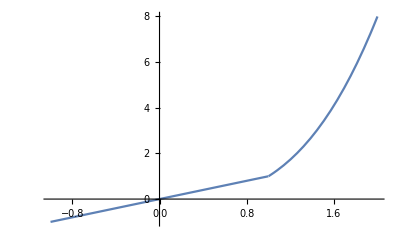

```mathematica
Plot[takeoff[y],{y,-1, 2}]
```

Unlike other Mathematica functions, the arguments to If are not all evaluated first and then passed in to If. Only the first argument is evaluated -- if it returns True the second argument is evaluated and its value is returned, but the third argument is never evaluated. If it returns False, the third argument is evaluated but the second is not. If the arguments are expressions whose evaluation has side effects, like those involving Print, the side effects will not occur as they would in arguments to a normal function:

```mathematica
If[3>7, Print["It is!"], Print["It isn't!"]]
```

It isn't!

In peculiar Mathematica style, an If expression whose first argument does not evaluate to either True or False remains unevaluated:

```mathematica
If[z>10,1,0]
```

If[z>10,1,0]

Since z is not defined the whole expression remains unevaluated. If you provide If with a fourth argument, it will evaluate that in case the first argument doesn’t yield a Boolean:

```mathematica
If[z>10,1,0, Print["Error! z is not defined."]]
```

Error! z is not defined.

##### Practice: Using If

Write a function called reverseString that takes a single argument, tests whether it is a string (see StringQ), if so returns its reverse (see StringReverse), and if not prints an error message. Demonstrate your function on both a multi-character string and a non-string. ■

```mathematica
reverseString[n_] := If[ StringQ[n],
StringReverse[n] , 
Print["Not a string!"]]
```

```mathematica
reverseString[10]
```

Not a string!

```mathematica
reverseString["I love power naps"]
```

span rewop evol I

### Reading and writing to a file

At first, you’ll probably do a lot of simple code testing through the notebook interface, but when it comes to real data, you’ll need to read and write files. Let’s start with writing.

##### Incorporated reading

Read the documentation page tutorial/ReadingAndWritingWolframSystemFiles up to and including the section “Saving Definitions of Wolfram Language Objects”.  When you get to “Saving Wolfram Language Definitions in Encoded Form” you can abort your read.

Read tutorial/NamingAndFindingFiles. This is kind of long and you can read quickly through some of the latter parts. The important thing is to know what’s in this tutorial so you can come back to it later when you need to work with files more.

##### Practice: Reading and writing expressions

The functions Put (equivalent to >>) and Get (equivalent to <<) exchange expressions with files. Since everything in Mathematica is an expression, you can read and write anything this way. Copy the code you wrote for generating a random DNA sequence, paste it into a new cell below this one, and modify it to take a second argument which will specify a directory path. (If you don’t know how to specify directory paths as strings on your system, use the menu sequence Insert->File Path and select a file to see its pathname.) Each time you call the new function, it should either create the file specified in the input path and put the new random DNA sequence into it (this is what happens if the file does not yet exist) or, if there is already a file by that name, it should read in the file assuming that the contents is a DNA sequence represented as a string, generate a new sequence, append the new sequence on to the end of the old one, and write the new sequence back out again. Test whether the file specified by the path argument exists using FileExistsQ.  If so, use Get (which returns the value of the last expression in the file) to initialize your DNA string. Then generate n random DNA letters, adding them on to the end of the string you read in. Finally, write out the new string to the filename provided using Put, which will create the file if it doesn’t exist. Put will also overwrite whatever was in the file before, which in this case is what you want. Demonstrate that your program works by calling it twice with the same filename, adding 5 letters the first time and 7 second. Note that the only thing you are reading and writing to files is the DNA sequence -- the code can sit in a new cell write below this one.

```mathematica
randomDNA[n_,dirPath_] := 

With[{(*dir = SetDirectory[dirPath],*) 
nucleotides= List["A", "C", "G", "T"]}, 
Module[{output = nucleotides[[RandomInteger[{1,4}] ]]} 
,Do[
(*If[ FileExistsQ["functionRandomDNA2.m"],
Get["functionRandomDNA2.m"],
]*)
output = StringJoin[{output,nucleotides[[RandomInteger[{1,4}] ]]}]
, n-1]
;Print[output]
]
>> "functionRandomDNA2.m";

]
```

```mathematica
SetDirectory["C:\\Users\\Batman\\Documents\\FL2017\\cse587a"]
```

C:\Users\Batman\Documents\FL2017\cse587a

```mathematica
randomDNA[10,"C:\\Users\\Batman\\Documents\\FL2017\\cse587a"]
```

GTCAGCCCGA

```mathematica
randomDNA[5, "C:\\Users\\Batman\\Documents\\FL2017\\cse587a"]
```

CTTGT

### Syntax Coloring

Mathematica’s syntax coloring can often help you spot syntax errors.  

Undefined variables are colored dark blue:

```mathematica
Tabel[x,{x,1,10](* The function, Tabel, is colored blue because it undefined.  Tabel is probably a typo. *)
```

(Note: This cell won’t evaluate because the square brackets are not balanced, not because of the undefined variables.) Defined variables are colored black.  (Aside -- many of the variables in input cells in this notebook will appear blue even though they have been defined in previous input cells. That’s because cells are not evaluated by default when a notebook is loaded.) Once a variable is defined, all instances of the variable in the notebook will be defined and colored black.

```mathematica
Table[x,{x,1,10}
```

Mathematica notes missing arguments with a red carrot:

```mathematica
Table[x]
```

x

Mathematica highlights extra arguments in red:

```mathematica
Length[x,1]
```

Length::argx: Length called with 2 arguments; 1 argument is expected.

```mathematica
Length[x,1]
```

Length::argx: Length called with 2 arguments; 1 argument is expected.

Length[x,1]

Mathematica highlights arguments of user-defined functions in green:

```mathematica
f[x_]:= x^2
```

### Aborting calculations

To abort a calculation, on the menu select Evaluation -> Abort Calculation.  If this doesn’t work, try Evaluation -> Quit Kernel/Local.  This will stop the kernel, but it will not close your notebook.  To restart the kernel, evaluate a cell in the notebook.  A third option is to quit Mathematica; however, all unsaved changes will be lost.